Frequency: r[1]+(γ r[2])/(1-γ)

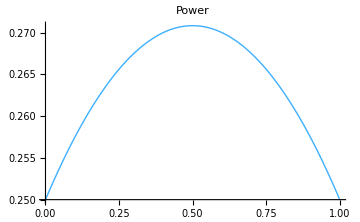
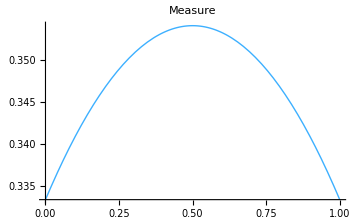
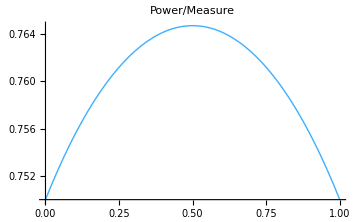

Frequency: r[1]+(γ r[3])/(1-γ)

-Graphics--Graphics--Graphics-

Frequency: r[1]+γ r[4]+(γ^2 r[5])/(1-γ)

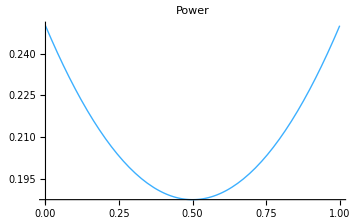
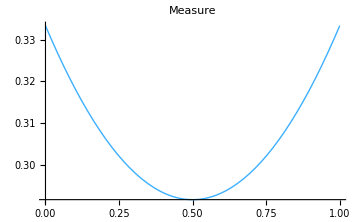
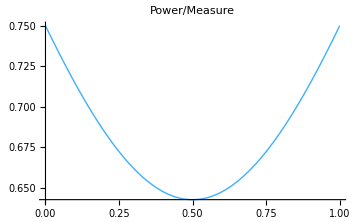

Total Power

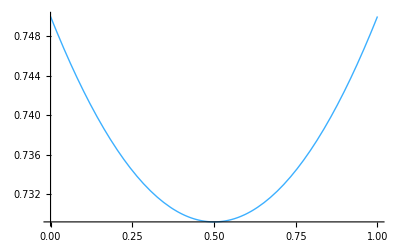

```mathematica
Clear[γ]
factor = (1-γ)/γ;
maxPlots = Length[powerOfEachFrequency];
t = Table[Plot[powerOfEachFrequency[[currentPlotIndex]]*factor,{γ,0,1}],{currentPlotIndex,1,maxPlots}];
For[currentPlotIndex = 1, currentPlotIndex <=maxPlots, currentPlotIndex++,
measure = finalMeasure[[currentPlotIndex]];
integration = powerOfEachFrequency[[currentPlotIndex]];
power = integration*factor;
Print["Frequency: ", equationList[[currentPlotIndex]]];
plotPower =Plot[power,{γ,0,1},PlotStyle->{{Thick,ColorData[96][1]}},PlotLabel->"Power" , ImageSize->Medium]; 
plotMeasure = Plot[measure,{γ,0,1},PlotStyle->{{Thick,ColorData[96][1]}}, PlotLabel->"Measure", ImageSize->Medium];
plotPowerByMeasure = Plot[power/measure,{γ,0,1},PlotStyle->{{Thick,ColorData[96][1]}}, PlotLabel->"Power/Measure", ImageSize->Medium];
Print[plotPower, plotMeasure, plotPowerByMeasure];
]
AllPower = finalPower*factor;
Print["Total Power"];
Print[Plot[AllPower,{γ,0,1},PlotStyle->{{Thick,ColorData[96][1]}}]]

(*
eq = powerOfEachFrequency[[1]];
eq2 = powerOfEachFrequency[[2]];
(*
eq = (γ (40+70 γ-25 γ^2-61 γ^3+20 γ^4+10 γ^5-40 γ^6-20 γ^7))/(120 (-1+γ)^2 (1+γ)^3);
eq2 = -(-1+5 γ+39 γ^2+45 γ^3+39 γ^4+35 γ^5+19 γ^6-5 γ^7-6 γ^8)/(120 (-1+γ) γ (1+γ)^2);
eq3 = (15+5 γ-80 γ^2+80 γ^3+265 γ^4-88 γ^5-285 γ^6+95 γ^8+5 γ^9-10 γ^10)/(120 (-1+γ)^2 γ (1+γ)^3);
*)
x = (Sqrt[5]-1)/2 //N;
eq3 = Simplify[finalPower]
(*
γ=0.99;
*)
factor = (1-γ)/γ;
Print["gamma =  ",γ];
Print["s1->s2->s2: Integration: ", eq,"| Power: ", eq*factor //Simplify //N];
Print["s1->s3->s4->s4: Integration: ", eq2 ,"| Power: ", eq2*factor //Simplify //N];
Print["FinalPower: Integration: ", eq3 ,"| Power: ", eq3*factor //Simplify //N];
(*
Show[Plot[eq*factor,{γ,0.9,1},PlotStyle->{{Thick,ColorData[96][1]}}], 
PlotRange->{{0,1},{0,6}}]
*)
Print["Power of s1->s2->s2 vs Gamma"]
Show[Plot[eq*factor,{γ,0,1},PlotStyle->{{Thick,ColorData[96][1]}}]]
Print["Power of s1->s3->s4->s5 vs Gamma"]

Show[
Plot[eq2*factor,{γ,0,1},PlotStyle->{{Dashed,ColorData[96][2]}}]]
Print["Overall Power"]
Show[
Plot[eq3*factor,{γ,0,1},PlotStyle->{{Thick,ColorData[96][3]}}]]
Print["Both"]

Show[Plot[eq*factor,{γ,0,1},PlotStyle->{{Thick,ColorData[96][1]}}], 
Plot[eq2*factor,{γ,0,1},PlotStyle->{{Thick,ColorData[96][2]}}],
PlotRange->{{0,1},{0.28,0.36}}]
(*
Show[Plot[eq3*factor,{γ,0,1},PlotStyle->{{Dotted,ColorData[96][3]}}]]
Show[Plot[eq*factor,{γ,0,x},PlotStyle->{{Thick,ColorData[96][1]}}], 
Plot[eq2*factor,{γ,x,2},PlotStyle->{{Thick,ColorData[96][2]}}],
Plot[eq3*factor,{γ,0,2},PlotStyle->{{Thick,ColorData[96][3]}}],
PlotRange->{{0,2},{-1,1}}]
*)
*)
```